5.13423×10^8+6.09118×10^7 x

5.13423×10^8+(2.3981×10^9)/h

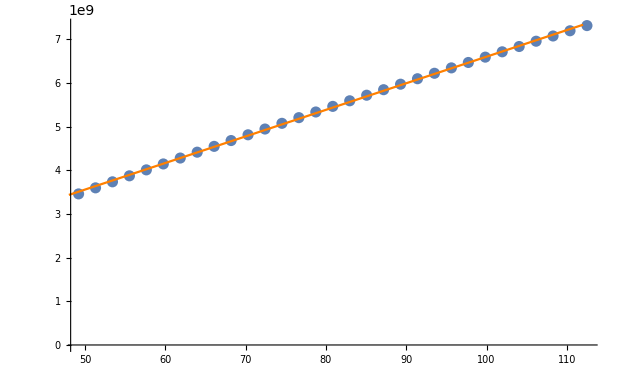

```mathematica
rawdata=Import["H:\\Users\\chz78\\Data\\HFSS\\cavity_frequency_sweep_a03_pinr01.csv"];
data=Delete[rawdata,1];
inverhight=data[[All,2]];
freq=data[[All,3]];
reshapedata=Transpose[{inverhight,freq}];
dataplot=ListPlot[reshapedata];
fit[x_]:=Fit[reshapedata,{1,x},x];
fitplot=Plot[Evaluate[fit[x]],{x,48,112},PlotStyle->Orange];
fit[x]
fit[x]/.x-> (1/(h *0.0254))
Show[dataplot,fitplot]
```

```mathematica
1/0.35/0.0254
```

112.486